Langevin

1.85195×10^-14 √((-Sin[348.703 √f]+Sinh[348.703 √f])/(√f (804248.-78.7594 f^2)^2 (-Cos[348.703 √f]+Cosh[348.703 √f])))

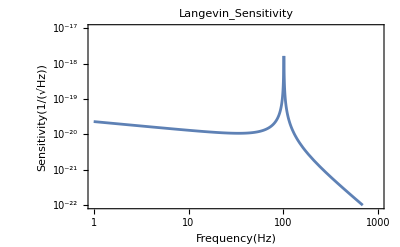

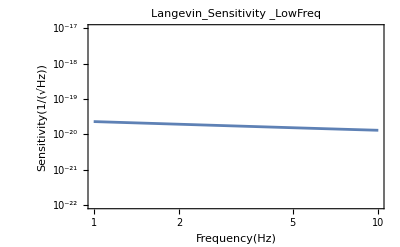

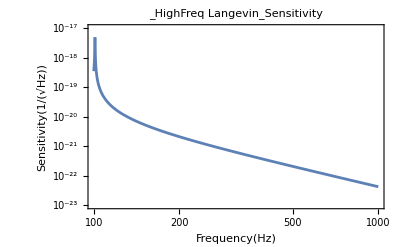

```mathematica
(*Langevin*)
LangevinPS=((s E0)/(s E0-M ω^2 L))^2(2 kB T^2 α^2 L^3)/κ 1/(kd L)(Sinh[2 kd L]-Sin[2 kd L])/(Cosh[2 kd L]-Cos[2 kd L])/.
{k2->√((ρ ω^2)/(s E0)),kd->√(ω/(2χ)),χ->κ/(ρ Cv)}/.
{kB->1.38 10^-23,T->300,α->5.0*10^(-6),L->0.35,κ->0.00008,ρ->0.008,Cv->7.9 10^2,ω->2π f,E0->4.0*10^(11),M->22.8/4,s->0.0016^2 Pi/4,χ->1.266*10^-5};
LangevinSensi=Sqrt[LangevinPS] / 200 / 3000
LangevinSensiG=LogLogPlot[LangevinSensi,{f,1,1000},PlotRange->{{1,1000},{10^-22,10^-17}},PlotLabel->Langevin_Sensitivity,Frame->True,FrameLabel->{Frequency[Hz],Sensitivity[1/Sqrt[Hz]]}]
(*Langevin Low Freq*)
LangevinSensiG10=LogLogPlot[LangevinSensi,{f,1,10},PlotRange->{{1,10},{10^-22,10^-17}},PlotLabel->Langevin_Sensitivity_LowFreq,Frame->True,FrameLabel->{Frequency[Hz],Sensitivity[1/Sqrt[Hz]]}]
(*Langevin High Freq*)
LangevinSensiG10=LogLogPlot[LangevinSensi,{f,100,1000},PlotRange->{{100,1000},{10^-23,10^-17}},PlotLabel->Langevin_Sensitivity_HighFreq,Frame->True,FrameLabel->{Frequency[Hz],Sensitivity[1/Sqrt[Hz]]}]
```

Levin

1.30135×10^-21 √((f^2 (3.57907×10^-26 f^2-(3.07918×10^-28 f^(3/2) (-Sin[348.703 √f]+Sinh[348.703 √f]))/(-Cos[348.703 √f]+Cosh[348.703 √f])))/((-0.000626657 √(f^2) Cos[0.00021933 √(f^2)]+0.000279798 f^2 Sin[0.00021933 √(f^2)])^2))

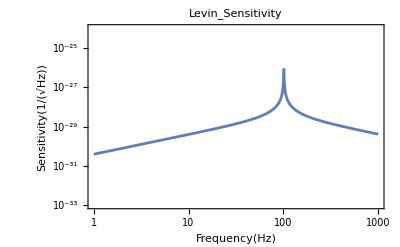

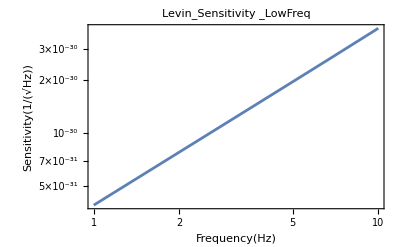

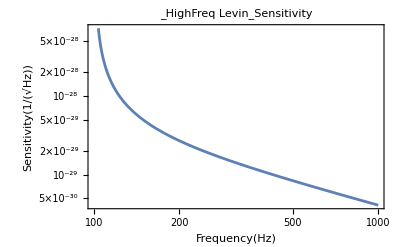

```mathematica
(*自分のファイル　Levin*)

LevinPS=(4 kB T^2 α^2)/κ(k2/((M ω^2)/(s E0)Sin[k2 L]-k2 Cos[k2 L]))^2(L^3/3(k2/kd)^4-L^2/2 k2^4/kd^5(Sinh[2 kd L]-Sin[2 kd L])/(Cosh[2 kd L]-Cos[2 kd L]))/.
{k2->√((ρ ω^2)/(s E0)),kd->√(ω/(2χ)),χ->κ/(ρ Cv)}/.
{kB->1.38 10^-23,T->300,α->5.0*10^(-6),L->0.35,κ->0.00008,ρ->0.008,Cv->7.9 10^2,ω->2π f,E0->4.0*10^(11),M->22.8/4,s->0.0016^2 Pi/4,χ->1.266*10^-5};
LevinSensi=Sqrt[LevinPS] / 200 / 3000
LevinSensiG=LogLogPlot[LevinSensi,{f,1,1000},PlotRange->{{1,1000},{10^-33,10^-24}},PlotLabel->Levin_Sensitivity,Frame->True,FrameLabel->{Frequency[Hz],Sensitivity[1/Sqrt[Hz]]}]

(*Levin Low Freq*)
LevinSensiG10=LogLogPlot[LevinSensi,{f,1,10},(*PlotRange->{{1,10},{10^-28,10^-26}},*)PlotLabel->Levin_Sensitivity_LowFreq,Frame->True,FrameLabel->{Frequency[Hz],Sensitivity[1/Sqrt[Hz]]}]
(*Levin High Freq*)
LevinSensiG10=LogLogPlot[LevinSensi,{f,100,1000},(*PlotRange->{{1,10},{10^-28,10^-26}},*)PlotLabel->Levin_Sensitivity_HighFreq,Frame->True,FrameLabel->{Frequency[Hz],Sensitivity[1/Sqrt[Hz]]}]
```

GabSensiはadmittance_result_231012and14note.nbから

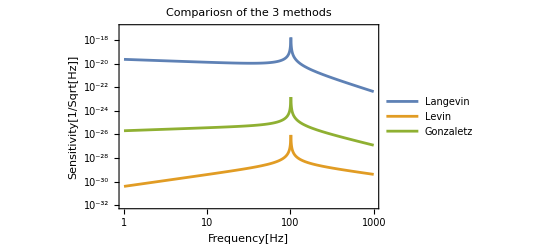

```mathematica
LogLogPlot[{LangevinSensi,LevinSensi,GabSensi},{f,1,1000},PlotRange->{{1,1000},{10^-32,10^-17}},PlotLegends->Placed[{"Langevin","Levin","Gonzaletz"},{0.28,0.61}],PlotLabel->"Compariosn of the 3 methods",Frame->True,FrameLabel->{"Frequency[Hz]","Sensitivity[1/Sqrt[Hz]]"},GridLinesStyle->LightGray,GridLines->Full]
```